```mathematica
asympt[n_]:= n - Floor[Sqrt[2n+0.25] - 0.5] / n - ( n - Floor[Sqrt[2n+0.25] - 0.5]) + 1
```

```mathematica
asympt[6]
```

7/2

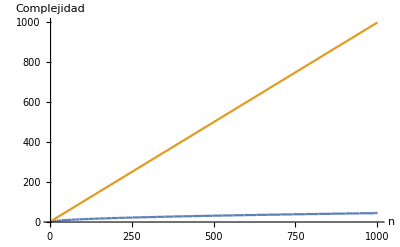

```mathematica
Plot[{asympt[x],x},{x,3,1000},AxesLabel->{"n","Complejidad"}]
```

```mathematica
Table[Binomial[Binomial[n,2],k] * k,{k,3,10}]
```

{1/4 (-1+n) n (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n),1/12 (-1+n) n (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n),1/48 (-1+n) n (-4+1/2 (-1+n) n) (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n),6 Binomial[1/2 (-1+n) n,6],7 Binomial[1/2 (-1+n) n,7],8 Binomial[1/2 (-1+n) n,8],9 Binomial[1/2 (-1+n) n,9],10 Binomial[1/2 (-1+n) n,10]}

```mathematica
complx=Sum[Binomial[Binomial[n,2],k] * k,{k,1,10}]
```

1/2 (-1+n) n+1/2 (-1+n) n (-1+1/2 (-1+n) n)+1/4 (-1+n) n (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/12 (-1+n) n (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/48 (-1+n) n (-4+1/2 (-1+n) n) (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+6 Binomial[1/2 (-1+n) n,6]+7 Binomial[1/2 (-1+n) n,7]+8 Binomial[1/2 (-1+n) n,8]+9 Binomial[1/2 (-1+n) n,9]+10 Binomial[1/2 (-1+n) n,10]

```mathematica
f[n_]:=1/2 (-1+n) n+1/2 (-1+n) n (-1+1/2 (-1+n) n)+1/4 (-1+n) n (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/12 (-1+n) n (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+1/48 (-1+n) n (-4+1/2 (-1+n) n) (-3+1/2 (-1+n) n) (-2+1/2 (-1+n) n) (-1+1/2 (-1+n) n)+6 Binomial[1/2 (-1+n) n,6]+7 Binomial[1/2 (-1+n) n,7]+8 Binomial[1/2 (-1+n) n,8]+9 Binomial[1/2 (-1+n) n,9]+10 Binomial[1/2 (-1+n) n,10]
AsymptoticLessEqual[f[n],n^12,n->Infinity]
```

False

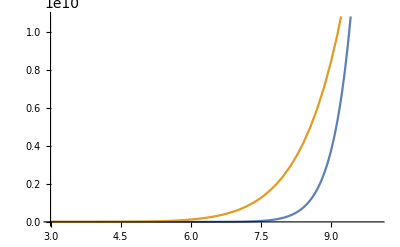

```mathematica
Plot[{f[n],n^10.4},{n,3,10}]
```

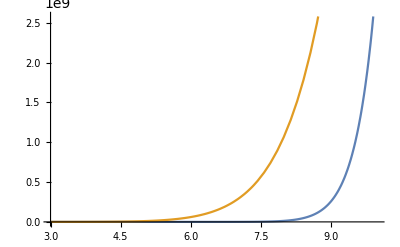

```mathematica
Plot[{Binomial[Binomial[n,2],10],n^10},{n,3,10}]
```